Lecture Intro AceFEM
Notebook for Exercises 
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 02 November 2021 - Contact: m.marino@ing.uniroma2.it

# Element Codes

## T1LE - Linear elasticity

### Initialization

```mathematica
<<AceGen`;
SMSInitialize["T1LE","Environment"-> "AceFEM","Mode"-> "Optimal"];
SMSTemplate["SMSTopology"->"T1",
(*Numerical Integration*) "SMSDefaultIntegrationCode"->35,
(*35 -Graphics-*)
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson"}, "SMSDefaultData" -> {1,0.49},
(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True,
"SMSNoElementData" -> 3];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(* Equivalent to: SMSInteger[es$$["id", "NoIntPoints"]] *)
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
N1⊨1-ξ-η;
N2⊨ξ;
N3⊨η;
ℕh⊨{N1, N2, N3};

(*ISOPARAMETRIC MAPPING*)
𝕏⊨SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ2D⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
ℍ⊨{{ℍ2D⟦1,1⟧,ℍ2D⟦1,2⟧,0},{ℍ2D⟦2,1⟧,ℍ2D⟦2,2⟧,0},{0,0,0}};
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];
{λ,μ}⊢SMSHookeToLame[Ee,ν];
Ψe⊨ λ/2 Tr[𝔻]^2+μ Tr[𝔻.𝔻];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];

SMSDo[Ig,1,nip];

ElementDefinitions[Ig];

SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];

(* Initial creation on aleatory multivalue variables: total forces *)
SMSM[Fxx, 0];
SMSM[Fyy, 0];
SMSM[Fxy,0];


SMSDo[Ig,1,nip, 1, {Fxx, Fyy, Fxy} ];

ElementDefinitions[Ig];
σ⊨SMSD[Ψe,𝔻,"Symmetric"->True];

(* Creazione di nuove istanze dalle precedentemente create variabili ausiliarie *) 
SMSS[Fxx, Fxx + Jed wgp σ⟦1, 1⟧];
SMSS[Fyy, Fyy + Jed wgp σ⟦2, 2⟧];
SMSS[Fxy, Fxy + Jed wgp σ⟦1, 2⟧];


SMSIO[
{"Dxx"->𝔻⟦1,1⟧,"Dxy"->𝔻⟦1,2⟧,"Dyy"->𝔻⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧}
,"Export to","Integration point post"[Ig]];

SMSEndDo[{Fxx, Fyy, Fxy}];

SMSR[Ftxx, Fxx];
SMSR[Ftyy, Fyy];
SMSR[Ftxy, Fxy];

(* Esportazione dei 3 dati d'interesse per l'elemento come vettore riga*) 
SMSExport[{Ftxx, Ftyy, Ftxy}, Table[ed$$["Data", i], {i, 1, SMSNoElementData}]];
𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
(*SMTElementData[element number, "Data"]
ed$$["Data",i]*)
```

### Code generation

```mathematica
SMSWrite[];
```

File: T1LE.c  Size: 7768  Time: 3
Method | SKR | SPP
No.Formulae | 47 | 37
No.Leafs | 781 | 633

# FEM Simulations

## Cook' s Membrane

```mathematica
<<AceGen`;
<<AceFEM`;
```

### Definition of Mesh, Loads and Boundary Conditions

{810,599}

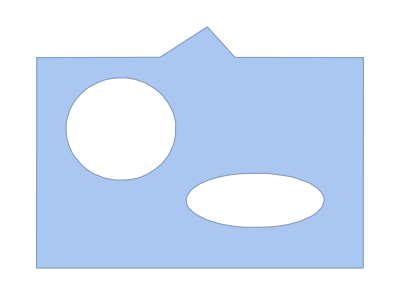

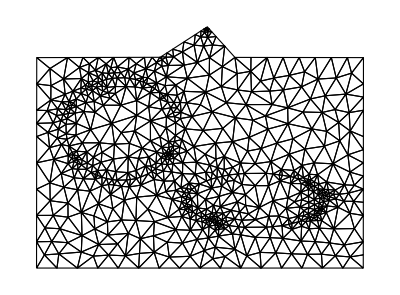

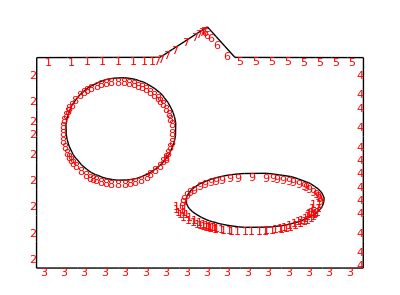

```mathematica
xc1=Lx/4;
yc1=Ly/4;
xc2=Lx/8;
L=1.2;
Lx = L; 
Ly = L; 
𝔻bc = {{a,c},{c,b}};
a = 1;
b =0 ;
c = 0; 
(*
Rc = 0.1784;
*)
Rc=0.250/2;


(*
mesh=ToElementMesh[Ω,"RegionHoles"->None,"MeshOrder"->1,"MaxCellMeasure"->0.001];
%["Wireframe"]
*)
(*im=-Graphics-;*)
im=-Graphics-;

dim=ImageDimensions[im]
mesha=ImageMesh[im]
(*
mesh=ToElementMesh[im,   "RegionHoles" -> None(*,"RegionMarker"->{{{2,2},1},{{540/3, 2*348/3},2}}*),"MeshOrder"->1,"MaxBoundaryCellMeasure"->1]["Wireframe"]*)

mesh=ToElementMesh[mesha,"RegionHoles"->None,"RegionMarker"->{{{2,2},1},{{dim⟦1⟧/3, 2*dim⟦2⟧/3},2},{{2*dim⟦1⟧/3,dim⟦2⟧/3},2}},"MeshOrder"->1,"MaxBoundaryCellMeasure"->1];
%["Wireframe"]
mesh["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Red]]
(*mesh=ToElementMesh[-Graphics-,"RegionHoles"->None,"RegionMarker"->{{{2,2},1},{{540/3, 2*348/3},2}},"MeshOrder"->1,"MaxBoundaryCellMeasure"->1];
%["Wireframe"]*)
(*
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->{{{Lx/8,Ly/8},1},
{{0xc1,4yc1},2},
{{1 xc1,4yc1},2},
{{2 xc1,4yc1},2},
{{3 xc1,4yc1},2},
{{4 xc1,4yc1},2},
{{1xc2,3yc1},2},
{{(xc2+xc1),3yc1},2},
{{(xc2+2 xc1),3yc1},2},
{{(xc2+3 xc1),3yc1},2}
},"MeshOrder"->1,"MaxCellMeasure"->0.001];
%["Wireframe"]
*)
```

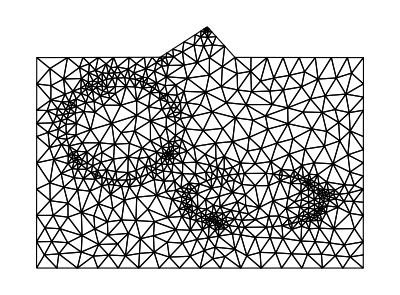

-Graphics-

```mathematica
<<AceFEM`;

SMTInputData[];
SMTAddDomain[
{"T1 matrix","T1LE",{"E *"-> 10^4,"ν *"->0.3}},
{"T1 inc 1","T1LE",{"E *"-> 10^2,"ν *"->0.3}},
{"T1 inc 2","T1LE",{"E *"->10^6,"ν *"->0.3}}
];
SMTAddMesh[mesh,{{"T1",1}->"T1 matrix",{"T1",2}->"T1 inc 1",{"T1",3}->"T1 inc 2"}];
SMTAddEssentialBoundary[nodestest, 1->Function[{n, X, Y}, Y], 2 ->Function[{n, X, Y}, Y],"Set"->True]

(*
SMTAddEssentialBoundary[Line[{{0,0},{0,dim⟦2⟧}}], 1->Function[{n, X, Y},b Y], 2 ->Function[{n, X, Y},c Y],"Set"->True];

SMTAddEssentialBoundary[Line[{{0,Ly},{Lx,Ly}}], 1 -> Function[{n, X, Y}, b*Ly+a*X], 2->Function[{n, X, Y}, c*Ly+b*X],"Set"->True];
SMTAddEssentialBoundary[Line[{{Lx,Ly},{Lx,0}}], 1 ->Function[{n, X, Y}, a*Lx+b*Y], 2->Function[{n, X, Y}, b*Lx+c*Y], "Set"->True];
SMTAddEssentialBoundary[Line[{{0,0},{Lx,0}}], 1 ->Function[{n, X, Y},a*X], 2-> Function[{n, X, Y}, b*Lx], "Set"->True];
*)
SMTAnalysis[];
SMTShowMesh["NodeMarks"->True,"BoundaryConditions"->True]
nodestest=Intersection[SMTFindNodes["Y">=dim⟦2⟧-100||"Y"==0&],SMTFindNodes[{"BoundaryNodes"}]]
(*nodestest=Intersection[SMTFindNodes["X"<200&&"Y"==348||"X">400&&"Y"==348&],SMTFindNodes[{"BoundaryNodes"}]]*)
(*nodestest=SMTFindNodes["X"<200&&"Y"==348||"X">400&&"Y"==348&]*)
```

{{1,2,3,4,5,6,7,8,9,133,135,137,138,139,140,141,150,153,154,155,227,228,240,247,279,299,318,333,380,387,446,512,552,554,567,572,589,595,597,608,611,613,623,629,657,663,667,668},1→Function[{n,X,Y},Y],2→Function[{n,X,Y},Y],Set→True}

-Graphics-

{1,2,3,4,5,6,7,8,9,133,135,137,138,139,140,141,150,153,154,155,227,228,240,247,279,299,318,333,380,387,446,512,552,554,567,572,589,595,597,608,611,613,623,629,657,663,667,668}

### Solution algorithm (one load-step, one NR iteration)

```mathematica
SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"]

Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]
]
```

False

-Graphics-

### Solution algorithm (one load-step, NR loop)

```mathematica
tolNR=10^-8; maxNR = 15;

SMTNextStep["λ"->1];

While[
SMTConvergence[tolNR,maxNR],
SMTNewtonIteration[];
];
area=Lx*Ly;
nel = SMTNoElements;
Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area
```

{2.88246,1.37906,-1.38383×10^-9}

### Solution algorithm (fixed load-step, NR loop)

```mathematica
(*Direct Implementation*)
tolNR=10^-8;maxNR=15;

nstep=10;   Δλ=1/nstep;

Do[
SMTNextStep["Δλ"->Δλ];
While[
SMTConvergence[tolNR,maxNR]
,SMTNewtonIteration[];
];
,{i,1,nstep}]
```

```mathematica
(*Synthetic Implementation*)
tolNR=10^-8;maxNR=15; nstep=10;   Δλ=1/nstep;

SMTEquilibriumPaths[
"Method"->"Newton"
,"λMax"->1
,"Steps"->nstep
,"Tolerance"->tolNR
,"MaxIterations"->maxNR
,"Show"->False
];
```

### Solution algorithm (fixed load-step, NR loop) - WITH POSTPROCESSING

```mathematica
tolNR=10^-8;maxNR=15;
nstep=10;   Δλ=1/nstep;
qv={{0,0}};
Do[
SMTNextStep["Δλ"->Δλ];
While[
SMTConvergence[tolNR,maxNR]
,SMTNewtonIteration[];
];
 (*Postprocessing*)
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{L,H+Wy}]]}];
,{i,1,nstep}]
qv
ListLinePlot[qv,PlotMarkers-> "●",PlotStyle->Blue]
```

### Solution algorithm (adaptive load-step, NR loop)

```mathematica
(*Direct Implementation*)
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/10;ΔλMin=λMax/100;ΔλMax=λMax/2;

SMTNextStep["λ"->λ0];
While[
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive BC",targetNR,ΔλMin,ΔλMax,λMax}]
, SMTNewtonIteration[];
];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧,SMTStepBack[];];
SMTNextStep["Δλ"->step⟦2⟧]
];
```

```mathematica
(*Synthetic Implementation*)
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/10;ΔλMin=λMax/100;ΔλMax=λMax/2;
SMTEquilibriumPaths[
"Method"->"Newton"
,"λMax"->1
,"Steps"->"Adaptive"
,"Δλ0"->λ0
,"ΔλMin"->ΔλMin
,"ΔλMax"->ΔλMax
,"Tolerance"->tolNR
,"MaxIterations"->maxNR
,"OptimalIterations"->8
,"Show"->False
];
```

### Solution algorithm (adaptive load-step, NR loop) - WITH POSTPROCESSING

```mathematica
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/10;ΔλMin=λMax/100;ΔλMax=λMax/2;
qv={{0,0}};
SMTNextStep["λ"->λ0];
While[
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive BC",targetNR,ΔλMin,ΔλMax,λMax}]
, SMTNewtonIteration[];
];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧(*True if NOT converged*),
SMTStepBack[];
, (*Postprocessing*)
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{L,H+Wy}]]}];
];
SMTNextStep["Δλ"->step⟦2⟧]
];
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{L,H+Wy}]]}];
qv
ListLinePlot[qv,PlotMarkers-> "●",PlotStyle->Blue]
```